```mathematica
(*Mathematica*)
```

```mathematica
Clear[f,g,h,k,hh,kk,ll]
```

```mathematica
allColors=ColorData["Legacy"][[3,1]];
firstCols=Join[{"White","AliceBlue","LightBlue","Cyan","ManganeseBlue","DodgerBlue","Blue","Magenta","Purple","Pink","Tomato","Red","DarkOrange","Orange","DeepNaplesYellow","Gold","Banana","Yellow","LightYellow","Orange","Pink","LightPink","Yellow","LightYellow","LightPink","White","DeepNaplesYellow","Orange","DarkOrange","Tomato","Red","Tomato","Pink","LightPink","DeepNaplesYellow","Orange","DarkOrange","Tomato","White","Pink","Banana","LightBlue","DodgerBlue","Cyan","White","Purple","DarkOrchid","Magenta","ManganeseBlue","DeepNaplesYellow","Orange","DarkOrange","Tomato","GoldOchre","LightPink","Magenta","Green","DarkOrchid","LightSalmon","LightPink","Sienna","Green","Mint","DarkSlateGray","ManganeseBlue","SlateGray","DarkOrange","MistyRose","DeepNaplesYellow","GoldOchre","SapGreen","Yellow","Yellow","Tomato","DeepNaplesYellow","DodgerBlue","Cyan","Red","Blue","DeepNaplesYellow","Green","Magenta","DarkOrchid","LightSalmon","LightPink","Sienna","Green","Mint","DarkSlateGray","ManganeseBlue","SlateGray","DarkOrange","MistyRose","DeepNaplesYellow","GoldOchre","SapGreen","Yellow","LimeGreen"},{"White","AliceBlue","LightBlue","Cyan","ManganeseBlue","DodgerBlue","Blue","Magenta","Purple","Pink","Tomato","Red","DarkOrange","Orange","DeepNaplesYellow","Gold","Banana","Yellow","LightYellow","Orange","Pink","LightPink","Yellow","LightYellow","LightPink","White","DeepNaplesYellow","Orange","DarkOrange","Tomato","Red","Tomato","Pink","LightPink","DeepNaplesYellow","Orange","DarkOrange","Tomato","White","Pink","Banana","LightBlue","DodgerBlue","Cyan","White","Purple","DarkOrchid","Magenta","ManganeseBlue","DeepNaplesYellow","Orange","DarkOrange","Tomato","GoldOchre","LightPink","Magenta","Green","DarkOrchid","LightSalmon","LightPink","Sienna","Green","Mint","DarkSlateGray","ManganeseBlue","SlateGray","DarkOrange","MistyRose","DeepNaplesYellow","GoldOchre","SapGreen","Yellow","Yellow","Tomato","DeepNaplesYellow","DodgerBlue","Cyan","Red","Blue","DeepNaplesYellow","Green","Magenta","DarkOrchid","LightSalmon","LightPink","Sienna","Green","Mint","DarkSlateGray","ManganeseBlue","SlateGray","DarkOrange","MistyRose","DeepNaplesYellow","GoldOchre","SapGreen","Yellow","LimeGreen"}];
cols=ColorData["Legacy",#]&/@Join[firstCols,Complement[allColors,firstCols]];

cr[n_]:=cr[n]=cols[[n]];
```

```mathematica
(*Qudratic Sawtooth (cartoon) function*)
```

```mathematica
f[x_]=4*If[x>0&&x<=1/2,x^2,0.5-x^2/3-0.169]
```

4 If[x>0&&x≤1/2,x^2,0.5-x^2/3-0.169]

```mathematica
ff[x_]=f[Mod[Abs[x],1]]
```

4 If[Mod[Abs[x],1]>0&&Mod[Abs[x],1]≤1/2,Mod[Abs[x],1]^2,0.5-1/3 Mod[Abs[x],1]^2-0.169]

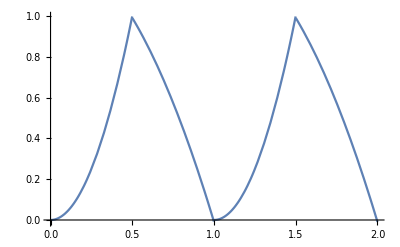

```mathematica
Plot[f[Mod[Abs[x],1]],{x,0,2}]
```

```mathematica
s0=N[Log[2]/Log[3]]
```

0.63093

```mathematica
hh[x_]=Sum[ff[3^k*(x-1/3)]/3^(s0*k),{k,0,20}];
```

```mathematica
kk[x_]=Sum[ff[3^k*(x)]/3^(s0*k),{k,0,20}];
```

```mathematica
ll[x_]=Sum[ff[3^k*(x+1/3)]/3^(s0*k),{k,0,20}];
```

```mathematica
nn=10000
```

10000

```mathematica
(*bb=Table[{ll[n/nn],hh[n/nn]},{n,0,nn}];
ListPlot[bb,ColorFunction->"Rainbow",ImageSize->Large]
cc=Table[{kk[n/nn],hh[n/nn]},{n,0,nn}];
ListPlot[cc,ColorFunction->"Rainbow",ImageSize->Large]*)
```

```mathematica
nn=100000
```

100000

```mathematica
aa=ParallelTable[{kk[n/nn],hh[n/nn],ll[n/nn]},{n,0,nn}];
```

```mathematica
Length[aa]
```

100001

```mathematica
g1=ListSurfacePlot3D[aa,ColorFunction->Hue,ImageSize->2000,PlotStyle->{PointSize->Small},Background->Black,ViewPoint->{2,2,2},Mesh->None,MaxPlotPoints->200];
```

```mathematica
(*dlst=ParallelTable[1+Mod[Floor[1+(1+Floor[24Norm[aa[[i]]]])/(Abs[Cos[Arg[aa[[i,1]]+I*aa[[i,2]]]]]+Abs[Sin[Arg[aa[[i,1]]+I*aa[[i,2]]]]])],Length[cols]],{i,Length[aa]}];
Min[dlst]
Max[dlst]
17
66
ptlst=Point[Developer`ToPackedArray[aa],VertexColors->Developer`ToPackedArray[cr/@dlst]];
g2=Rasterize[Graphics3D[{PointSize[.001],ptlst},AspectRatio->1,ImageSize->2000,Axes->False,Background->Black,PlotRange->All,ViewPoint->Front],RasterSize->2000,ImageSize->2000];
Export["biscuit_Quadratic_Sawtooth_3d_100000_noPicts.jpg",{g0,g2}]
"biscuit_Quadratic_Sawtooth_3d_100000_noPicts.jpg"*)
```

```mathematica
Clear[g2]
```

```mathematica
g2=Show[g0,ViewPoint->Above];
```

```mathematica
g3=Show[g0,ViewPoint->{1.3, -2.4, 2.}];
```

```mathematica
g4=Show[g0,ViewPoint->{0, -2, 2}];
```

```mathematica
Export["biscuit_Quadratic_Sawtooth_ListSurfacePlot3D_3d_100000_grid.jpg",GraphicsGrid[{{g0,g2},{g4,g3}},ImageSize->{{4000,4000}}]]
```

biscuit_Quadratic_Sawtooth_ListSurfacePlot3D_3d_100000_grid.jpg

```mathematica
(*end*)
```